```mathematica
<<mf23.m
```

```mathematica
Clear[c];
Clear[e];
ψ[z_]:=PolyGamma[z]; (* RHS is Mathematica-speak for the digamma function. *)
α[m_]:=(1/2)*(1/2-1/m);
β[m_]:=(1/2)*(1/2+1/m);
c[m_,ν_]:=Pochhammer[α[m],ν]*Pochhammer[β[m],ν]/(ν!)^2;
e[m_,ν_]:=Sum[1/(α[m]+p)+1/(β[m]+p)-2/(1+p),{p,0,ν-1}];
F[n_,m_,u_]:=Series[Sum[c[m,ν]*u^ν,{ν,0,n+1}],{u,0,n}];
Fstar[n_,m_,u_]:=Sum[c[m,ν]*e[m,ν]*u^ν,{ν,1,n}];
logA[m_]:=-2ψ[1]+ψ[1-α[m]]+ψ[1-β[m]]-π*Sec[π/m]; (* Raleigh's eq (10) *)
A[m_]:=Exp[logA[m]];
λ[m_]:=2*Cos[π/m]
```

#### From Raleigh p 108 eq 6 (abbreviating the F, F* inputs): 2πiτ/λ_m= - log J + F*(1/J)/F(1/J) - πi(b-bar) = - log J + F*(1/J)/F(1/J) + log A(m) = log(1/J) + F*(1/J)/F(1/J) + log A(m) . Taking exponentials, x_m =(1/J) exp( (F*(1/J)/F(1/J) ) A(m). Then x_m/A(m) = (1/J) exp( F*(1/J)/F(1/J). Viewing the RHS above as a power series in 1/J, invert it and get 1/J = a power series in x_m (Raleigh’s eq. 12 ), so J = 1/(the inverted power series)--but the uniformizing variable is X_m = x_m/A(m) ; not x_m. Below I inadvertently mixed the variables x and X, but tests indicate that this has no effect. Whether or not I replace x by X, the output is written (correctly ) in terms o f X.

```mathematica
ex[n_,m_,oneOverJ_]:=
Module[{a0,a1,a2,a3,a4,a5,a6,K},
a0=Series[Fstar[n,m,oneOverJ]/F[n,m,oneOverJ],{oneOverJ,0,n}];

a1=Series[Exp[a0],{oneOverJ,0,n}];

a2=Collect[oneOverJ*a1,oneOverJ];

a3=Series[a2,{oneOverJ,0,n}];
Return[a3]];

J[n_,m_,X_]:=Collect[Normal[Series[1/InverseSeries[ex[n,m,x],X],{X,0,n}]],X];

recipJ[n_,m_,X_]:=Collect[Normal[InverseSeries[ex[n,m,x],X]],X];

xJ[n_,m_,X_]:=Collect[X*J[n,m,X],X];

JnewCffList[n_,m_,x_]:=Module[{srs},
srs=xJ[n,m,x];
srs=srs/.x->x/A[m];
srs=Normal[srs];
Return[Round[CoefficientList[srs,x]]]]
```

```mathematica
fλNew3[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator),{X,0,n}],X];
Return[answer]]
```

#### The weight of f_λ at Hecke rank m is determined in Theorem 7 of Berndt in my paper; with outer exponent in Theorem 8 (my draft) altered from 1/(m-2) to 1 as above, the weight is 4 for all m. The cubes have weight12.

```mathematica
fλcubed[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator)^3,{X,0,n}],X];
Return[answer]]
```

```mathematica
diamondCuspFrm[n_,m_,X_]:=
Collect[fλcubed[n,m,X]*recipJ[n,m,X],X]
```

```mathematica
Print[diamondCuspFrm[6,3,X]]
```

X-X^2/72+(7 X^3)/82944-(23 X^4)/80621568+(805 X^5)/1486016741376-(7 X^6)/17832200896512-(17357786380025 X^7)/92442129447518208-(914340879836245 X^8)/19967499960663932928-(98097607881457445 X^9)/30670079939579800977408-(3572540741339744345 X^10)/79496847203390844133441536-(7036935371751179195 X^11)/22895091994576563110431162368-(371440349809702285 X^12)/274741103934918757325173948416

```mathematica
Print[
Series[
Collect[
(1/1728)*diamondCuspFrm[6,3,X]/.X->1728*X,X
],{X,0,6}]
];
Print[Table[RamanujanTau[n],{n,1,6}]]
```

X-24 X^2+252 X^3-1472 X^4+4830 X^5-6048 X^6+O[X]^7

{1,-24,252,-1472,4830,-6048}

```mathematica
srs=Normal[Series[diamondCuspFrm[10,3,x],{x,0,10}]];
c1=Coefficient[srs,x,1];
series=Collect[srs/c1,x];
Print[srs];
Print[series]
```

x-x^2/72+(7 x^3)/82944-(23 x^4)/80621568+(805 x^5)/1486016741376-(7 x^6)/17832200896512-(2093 x^7)/3327916660110655488+(55 x^8)/29951249940995899392-(1403 x^9)/981442558066553631277056-(805 x^10)/953962166440690129601298432

x-x^2/72+(7 x^3)/82944-(23 x^4)/80621568+(805 x^5)/1486016741376-(7 x^6)/17832200896512-(2093 x^7)/3327916660110655488+(55 x^8)/29951249940995899392-(1403 x^9)/981442558066553631277056-(805 x^10)/953962166440690129601298432

```mathematica
stream=OpenWrite["run24apr21no1"];
For[m=2,m<300,m++;
srs=Normal[Series[diamondCuspFrm[100,m,x],{x,0,100}]];
Write[stream,{m,srs}]];
Close[stream]
```

run24apr21no1

#### Dividing by J - constant introduces no singularities except at the constant, and they have weight zero and transform like γ = 1. Formally, the q_m - series for 1/(J_m - constant) introduces no singularities at all . Also note that f is in M (λ, k, -1) = > f^2 is in M (λ, 2 k, +1) . Hence in Berndt' s theorem 7 (my draft numbering) f_i^2 is in M (λ, 4m/(m - 2), +1) and f_i^(2m - 4) is in M (λ, 4m, +1) . So (for m = 3) f_i^2 is in M (λ, 12, +1) and so (for m = 3 again) f_i^2/J_ 3 should be a weight 12 cusp form .

```mathematica
fi[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator)^(1/(m-2)),{x,0,n}];
Return[answer]]
```

```mathematica
fiNo2[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Normal[Series[(numerator/denominator),{x,0,n}]];
Return[answer]]
```

```mathematica
fiNo3[n_,m_,x_]:=
Module[{kay,answer1,answer2,djaydx,oneovrjayminus1},
kay=K[n+1,m,x];
djaydx=-D[kay,x]/kay^2;
oneovrjayminus1=1+1/(kay-1);
answer1=x^m*djaydx^m*kay^(m-1)*oneovrjayminus1;
answer2=Normal[Series[answer1,{x,0,n}]];
Return[answer2]]
```

```mathematica
fiNoOuterExponent[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator),{x,0,n}];
Return[answer]]
```

```mathematica
n=5;
For[m=2,m<7,m++;
srs=fi[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
Print["=========================================================="];
Print["m: ",m];
Print[srs]]
```

==========================================================

m: 3

x-(73 x^2)/72+(36871 x^3)/82944-(10118543 x^4)/80621568+(42943611685 x^5)/1486016741376

==========================================================

m: 4

x-(33 x^2)/32+(7171 x^3)/16384-(29151 x^4)/262144+(46653335 x^5)/2147483648

==========================================================

m: 5

Piecewise[{{(-1)^(2/3) x-209/200 (-1)^(2/3) x^2+(281879 (-1)^(2/3) x^3)/640000-(20589239 (-1)^(2/3) x^4)/192000000+(190273302301 (-1)^(2/3) x^5)/9830400000000, Im[(39 x)/40-(19227 x^2)/64000+(618839 x^3)/25600000+(213623709 x^4)/163840000000+(248538558957 x^5)/3276800000000000]≥0}, {(1/2-(ⅈ √3)/2)^2 x+209/800 (ⅈ+√3)^2 x^2-(281879 (ⅈ+√3)^2 x^3)/2560000+(20589239 (ⅈ+√3)^2 x^4)/768000000-(190273302301 (ⅈ+√3)^2 x^5)/39321600000000, True}}]

==========================================================

m: 6

x-(19 x^2)/18+(577 x^3)/1296-(33533 x^4)/314928+(418465 x^5)/22674816

==========================================================

m: 7

Piecewise[{{(-1)^(2/5) x-417/392 (-1)^(2/5) x^2+(1106647 (-1)^(2/5) x^3)/2458624-(7357411 (-1)^(2/5) x^4)/68841472+(876537704543 (-1)^(2/5) x^5)/48358655787008, Im[(95 x)/56-(28405 x^2)/25088+(50381635 x^3)/137682944-(94526260555 x^4)/1727094849536+(6412331516645 x^5)/2708084724072448]≥0}, {1/16 (1+√5-ⅈ √(2 (5-√5)))^2 x-(417 (1+√5-ⅈ √(2 (5-√5)))^2 x^2)/6272+(1106647 (1+√5-ⅈ √(2 (5-√5)))^2 x^3)/39337984-(7357411 (1+√5-ⅈ √(2 (5-√5)))^2 x^4)/1101463552+(876537704543 (1+√5-ⅈ √(2 (5-√5)))^2 x^5)/773738492592128, True}}]

```mathematica
n=5;
For[m=2,m<10,m=m+2;
srs=fi[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
Print["=========================================================="];
Print["m: ",m];
Print[srs]]
```

==========================================================

m: 4

x-(33 x^2)/32+(7171 x^3)/16384-(29151 x^4)/262144+(46653335 x^5)/2147483648

==========================================================

m: 6

x-(19 x^2)/18+(577 x^3)/1296-(33533 x^4)/314928+(418465 x^5)/22674816

==========================================================

m: 8

x-(137 x^2)/128+(119171 x^3)/262144-(5420513 x^4)/50331648+(9922407255 x^5)/549755813888

==========================================================

m: 10

x-(27 x^2)/25+(4621 x^3)/10000-(10277 x^4)/93750+(227363 x^5)/12500000

```mathematica
n=5;
For[m=2,m<10,m=m+2;
srs=fi[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
srs=srs/.x->2^6*m^3*x;
Print["=========================================================="];
Print["m: ",m];
Print[srs]]
```

==========================================================

m: 4

4096 x-17301504 x^2+30077353984 x^3-31300647911424 x^4+25046818509291520 x^5

==========================================================

m: 6

13824 x-201719808 x^2+1176175116288 x^3-3888624735092736 x^4+9317169449674997760 x^5

==========================================================

m: 8

32768 x-1149239296 x^2+15994860863488 x^3-(372494817000685568 x^4)/3+681862634525090119680 x^5

==========================================================

m: 10

64000 x-4423680000 x^2+121136742400000 x^3-(5517422362624000000 x^4)/3+19530332986408960000000 x^5

```mathematica
n=5;
For[m=2,m<10,m=m+2;
srs=fi[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
srs=srs/.x->2^6*m^3*x;
c1=Coefficient[srs,x,1];
srs=Collect[srs/c1,x];
Print["=========================================================="];
Print["m: ",m];
Print[srs]]
```

==========================================================

m: 4

x-4224 x^2+7343104 x^3-7641759744 x^4+6114945925120 x^5

==========================================================

m: 6

x-14592 x^2+85082112 x^3-281295192064 x^4+673985058570240 x^5

==========================================================

m: 8

x-35072 x^2+488124416 x^3-(11367639678976 x^4)/3+20808796219637760 x^5

==========================================================

m: 10

x-69120 x^2+1892761600 x^3-(86209724416000 x^4)/3+305161452912640000 x^5

```mathematica
n=20;
m=3;
srs=fi[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
srs=srs/.x->2^6*m^3*x;
c1=Coefficient[srs,x,1];
srs=Collect[srs/c1,x];
Print[CoefficientList[srs,x]]
```

{0,1,-1752,1327356,-647586752,257661670110,-91232051575968,29954198551543448,-9328495120349652480,2793796864526004274197,-811936298779546210082640,230405639216897418010749012,-64128227399842224348646486272,17564361932436534860230986313526,-4746168271382967848129327576145984,1267770309338241784828659667380867720,-335280365698260901501578151501064597504,87901917117365539108730453662589095550898,-22869906861087468896727023132865467777150904,5909931979240012559768932259883987988887891500,-1517988120100629861321073833088924328846378401920}

```mathematica
n=20;
m=4;
srs=fi[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
srs=srs/.x->2^6*m^3*x;
c1=Coefficient[srs,x,1];
srs=Collect[srs/c1,x];
Print[CoefficientList[srs,x]]
```

{0,1,-4224,7343104,-7641759744,6114945925120,-4183095309762560,2579055585404125184,-1476808502025052487680,800203959984940356993024,-415409295039151003884584960,208404755828970033002974281728,-101676134153347557246339525902336,48467230224939394645932160694878208,-22654745402858743327890716061390077952,10413062297321587396762438431275420221440,-4717213735124668693351368191105308265807872,2109964241427021195763378510102121905473454080,-933255631589825143361821604052421410150162628608,408701353713186541485738512125549415363848769110016,-177398126480286613777710697935613484413748936777400320}

```mathematica
n=10;
m=3;
srs=fi[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
c1=Coefficient[srs,x,1];
srs=Collect[srs/c1,x];
Print[CoefficientList[srs,x]]
```

{0,1,-73/72,36871/82944,-10118543/80621568,42943611685/1486016741376,-105592652287/17832200896512,3744274818942931/3327916660110655488,-6073239010644305/29951249940995899392,34491319315135855237/981442558066553631277056,-5638446519302404236685/953962166440690129601298432}

### Might get a nicer result by fixing the weight.

```mathematica
fiWt6[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
power=3/m;
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator)^power,{x,0,n}];
Return[answer]]
```

```mathematica
n=20;
m=3;
srs=fiWt6[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
srs=srs/.x->2^6*m^3*x;
c1=Coefficient[srs,x,1];
srs=Collect[srs/c1,x];
Print[CoefficientList[srs,x]]
```

{0,1,-1752,1327356,-647586752,257661670110,-91232051575968,29954198551543448,-9328495120349652480,2793796864526004274197,-811936298779546210082640,230405639216897418010749012,-64128227399842224348646486272,17564361932436534860230986313526,-4746168271382967848129327576145984,1267770309338241784828659667380867720,-335280365698260901501578151501064597504,87901917117365539108730453662589095550898,-22869906861087468896727023132865467777150904,5909931979240012559768932259883987988887891500,-1517988120100629861321073833088924328846378401920}

```mathematica
n=5;
For[m=2,m<10,m=m+2;
Print["=========================================================="];
srs=fiWt6[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
srs=srs/.x->2^6*m^3*x;
c1=Coefficient[srs,x,1];

srs=Collect[srs/c1,x];

Print["m: ",m];
Print["c1: ",c1];
Print[srs]]
```

==========================================================

m: 4

c1: 4096

x-5504 x^2+12647424 x^3-16617570304 x^4+15183025930240 x^5

==========================================================

m: 6

c1: 13824

x-23808 x^2+239026176 x^3-1342336663552 x^4+4824302151008256 x^5

==========================================================

m: 8

c1: 32768

x-63232 x^2+1705537536 x^3-(77767582416896 x^4)/3+(751561028581457920 x^5)/3

==========================================================

m: 10

c1: 64000

x-131840 x^2+7472332800 x^3-(721115152384000 x^4)/3+(14794244698931200000 x^5)/3

```mathematica
stream=OpenWrite["run5may21no1"];
n=12;
For[m=2,m<120,m=m+2;
srs=fiWt6[n,m,x]^2/J[n,m,x];
srs=Series[srs,{x,0,n}];
srs=Normal[srs];
srs=srs/.x->2^6*m^3*x;
c1=Coefficient[srs,x,1];

srs=Collect[srs/c1,x];

Write[stream,{m,srs}]];
Close[stream]
```

$Aborted

run5may21no1

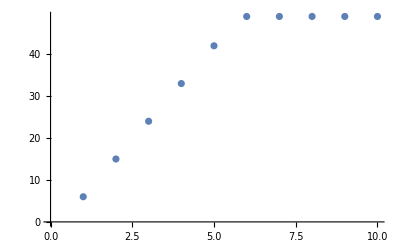

{{1,6},{2,15},{3,24},{4,33},{5,42},{6,49},{7,49},{8,49},{9,49},{10,49}}

run5may21no2

```mathematica
stream=OpenRead["run5may21no1"];
list=ReadList[stream];
Close[stream];

wstream=OpenWrite["run5may21no2"];

degrees={};
For[n=0,n<10,n++;
data={};
For[k=2,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];

Write[wstream,{n,ip}];

AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];

Close[wstream]
```

```mathematica
stream=OpenRead["run5may21no2"];
list=ReadList[stream];
Close[stream];
numerators={};
denominators={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoMonics[poly];
numericalterm=fim[[1]];
numerator=Numerator[numericalterm];
denominator=Denominator[numericalterm];
AppendTo[numerators,numerator];
AppendTo[denominators,denominator]];
Print["numerators:"];Print[numerators/64];
Print["denominators:"];Print[denominators]
```

numerators:

{
1,-10752,51363840,-144435052544,268086993223680,-542851644294421936523444224,90355342039953013814531963511518452946522783757497270272,-2535424865030753958919494255931211102153437583709338867254181810427068681516220416,243322339954772194542873158652708234876769292837249675175301463889585251006695846262364532780508628647936,-26418455001773823256083202279661066319656733597619188616485656590057713940411212250282162529294914018338078967862868333572390912}

denominators:

{1,1,1,1,1,375,30375,297675,165375,535815}

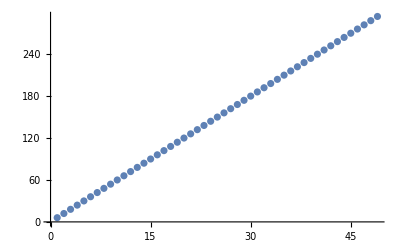

{{1,6},{2,12},{3,18},{4,24},{5,30},{6,36},{7,42},{8,48},{9,54},{10,60},{11,66},{12,72},{13,78},{14,84},{15,90},{16,96},{17,102},{18,108},{19,114},{20,120},{21,126},{22,132},{23,138},{24,144},{25,150},{26,156},{27,162},{28,168},{29,174},{30,180},{31,186},{32,192},{33,198},{34,204},{35,210},{36,216},{37,222},{38,228},{39,234},{40,240},{41,246},{42,252},{43,258},{44,264},{45,270},{46,276},{47,282},{48,288},{49,294}}

run11may21no4

```mathematica
stream=OpenRead["run24apr21no1"];
list=ReadList[stream];
Close[stream];

wstream=OpenWrite["run11may21no4"];

degrees={};
For[n=0,n<49,n++;
data={};
For[k=2,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];

Write[wstream,{n,ip}];

AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];

Close[wstream]
```

```mathematica
stream=OpenRead["run11may21no4"];
list=ReadList[stream];
Close[stream];
numericalterms={};
numerators={};
denominators={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoMonics[poly];
numericalterm=fim[[1]];
AppendTo[numericalterms,numericalterm]];
table=Table[(-1)^(n+1)*RamanujanTau[n],{n,1,49}];
Print[numericalterms/64-table]
```